### Построить график в логарифмическом масштабе: 1 Площадь/Население по всем странам мира 2 При наведении на страну должен показывать ее флаг

```mathematica
Cont=EntityList["Country"];
Ar=#[EntityProperty["Country","Area"]]&/@Cont;
Pop= #[EntityProperty["Country","Population"]]&/@Cont;
Flag=#[EntityProperty["Country","FlagImage"]]&/@Cont;
Name=CanonicalName[#]&/@Cont;
```

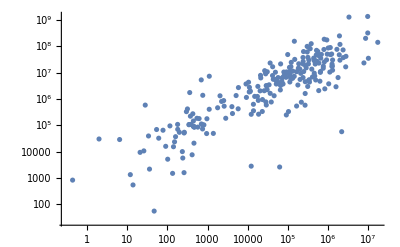

```mathematica
ListLogLogPlot[
Tooltip[{Ar[[#]],Pop[[#]]},Grid[{{Flag[[#]]},{Name[[#]]}}]]&/@Range[Length[Ar]] 
]
```

```mathematica
Ar=Entity["Country"][EntityProperty["Country","Area"]];
Pop=Entity["Country"][EntityProperty["Country","Population"]];
Flag=Entity["Country"][EntityProperty["Country","FlagImage"]];
Name=CanonicalName[EntityList["Country"]];
ListLogLogPlot[
Tooltip[{Ar[[#]],Pop[[#]]},Grid[{{Flag[[#]]},{Name[[#]]}}]]&/@Range[Length[Ar]] 
]
```

-Graphics-

### Построить таблицу по странам Европы+Россия+Турция: 1. Страна/Площадь / Население 2. Подписать колонки таблицы 3. Первая строка на светло синем фоне, остальные на светложелтом

```mathematica
ContE=EntityList[EntityClass["Country", "EuropeExtended"]];
ArE=#[EntityProperty["Country","Area"]]&/@ContE;
PopE= #[EntityProperty["Country","Population"]]&/@ContE;
NameE=CanonicalName[#]&/@ContE;
```

```mathematica
Tabl=Prepend[ Transpose[{NameE,ArE,PopE}],{"Страна","Площадь","Население"}];
Grid[Tabl,Frame->All,Background->{None,{LightBlue,{LightYellow}}}]
```

Страна | Площадь | Население
Albania | 28748. km^2 | 3248655 people
Andorra | 468. km^2 | 85458 people
Austria | 83871. km^2 | 8452081 people
Belarus | 207600. km^2 | 9469915 people
Belgium | 30528. km^2 | 10841093 people
BosniaHerzegovina | 51197. km^2 | 3726569 people
Bulgaria | 110879. km^2 | 7300838 people
Croatia | 56594. km^2 | 4369961 people
Cyprus | 9251. km^2 | 1153409 people
CzechRepublic | 78867. km^2 | 10611300 people
Denmark | 43094. km^2 | 5628958 people
Estonia | 45228. km^2 | 1337821 people
FaroeIslands | 1393. km^2 | 49709 people
Finland | 338145. km^2 | 5434241 people
France | 551500. km^2 | 64101308 people
Germany | 357022. km^2 | 81625599 people
Gibraltar | 6.5 km^2 | 29111 people
Greece | 131940. km^2 | 11470255 people
Guernsey | 78. km^2 | 65605 people
Hungary | 93028. km^2 | 9918377 people
Iceland | 103000. km^2 | 335631 people
Ireland | 70273. km^2 | 4682042 people
IsleOfMan | 572. km^2 | 86159 people
Italy | 301340. km^2 | 61175248 people
Jersey | 116. km^2 | 95732 people
Kosovo | 10887. km^2 | 1859203 people
Latvia | 64589. km^2 | 2218123 people
Liechtenstein | 160. km^2 | 37313 people
Lithuania | 65300. km^2 | 3264812 people
Luxembourg | 2586. km^2 | 536427 people
Macedonia | 25713. km^2 | 2071178 people
Malta | 316. km^2 | 421844 people
Moldova | 33851. km^2 | 3473640 people
Monaco | 2. km^2 | 30508 people
Montenegro | 13812. km^2 | 633506 people
Netherlands | 41543. km^2 | 16806723 people
Norway | 323802. km^2 | 5022555 people
Poland | 312685. km^2 | 38344752 people
Portugal | 92090. km^2 | 10705265 people
Romania | 238391. km^2 | 21289792 people
Russia | 1.70982×10^7 km^2 | 142400066 people
SanMarino | 61. km^2 | 32742 people
Serbia | 77474. km^2 | 7164132 people
Slovakia | 49035. km^2 | 5497156 people
Slovenia | 20273. km^2 | 2049112 people
Spain | 505370. km^2 | 47290504 people
Svalbard | 62045. km^2 | 2637 people
Sweden | 450295. km^2 | 9595619 people
Switzerland | 41277. km^2 | 7788196 people
Turkey | 783562. km^2 | 76190381 people
Ukraine | 603550. km^2 | 44457736 people
UnitedKingdom | 243610. km^2 | 63556184 people
VaticanCity | 0.44 km^2 | 839 people

### На карте Южной Америки закрасить страны в соответствии 1. с долей площади с/х земель 2. изменить цветовую палитру на другую стандартную

```mathematica
GeoRegionValuePlot[EntityClass["Country","SouthAmerica"]->"AgriculturalLandFraction"]
```

-Graphics-

```mathematica
GeoRegionValuePlot[EntityClass["Country","SouthAmerica"]->"AgriculturalLandFraction",ColorFunction->ColorData["SiennaTones"]]
```

-Graphics-

```mathematica
GeoRegionValuePlot[EntityClass["Country","SouthAmerica"]->"AgriculturalLandFraction",ColorFunction->(ColorData["SiennaTones"][1-#]&)]
```

-Graphics-

### Построить граф стран Европы: 1. По наличию общей границы 2. Найти на данном графе максимальные клики 3. Найти центральность по посредничеству графа

```mathematica
con=EntityList[ EntityClass["Country", "Europe"]];
border=Flatten[
Thread[#<->#[EntityProperty["Country", "BorderingCountries"]]]&/@con];

g=Graph[con,border,VertexLabels->"Name"];
mat=Normal[AdjacencyMatrix[g]]/.{x_/;x>0->1};
gb=AdjacencyGraph[VertexList[g],mat,VertexLabels->"Name"];
bc=BetweennessCentrality[g];
HighlightGraph[gb,VertexList[gb],VertexSize-> Thread[VertexList[gb]-> Rescale[bc]]]
```

-Graphics-